```mathematica
data1={{1981,3.89},{1982,5.22},{1983,2.62},{1986,5.01},{1987,5.63},{1989,4.25},{1990,4.64},{1991,5},{1992,4.41},{1997,5.1},{1998,4.8},{1999,5.61},{2001,4.65},{2002,6.39},{2004,5.3},{2005,4.4},{2006,5.11},{2007,3.93},{2008,4.69},{2009,5.13},{2010,4.14},{2012,4.4},{2014,4.89},{2015,5.03},{2016,6.48},{2018,4.97}};
tsm=TimeSeriesModelFit[data1,{"SARIMA",{{2,1,2},{6,0,2},5}}]
```

TemporalData::rsmplng: 数据没有均匀间隔，并且将自动采样到最小时间增量的解决方案 .

TimeSeriesModel[…]

```mathematica
Array[a,50,2018];
Array[b,50,2018];
Do[{a[n]=Part[tsm["PredictionLimits"][n],1],b[n]=Part[tsm["PredictionLimits"][n],2]},{n,2018,2067}]
u=Table[i*(2-j)+(j-1)*a[i],{i,2018,2067},{j,2}];
d=Table[i*(2-j)+(j-1)*b[i],{i,2018,2067},{j,2}];
```

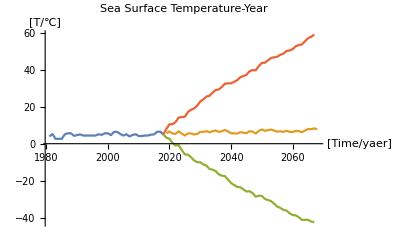

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{50}],u,d},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"Time","/","yaer"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Year],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```